```mathematica
source=RandomReal[1,10]
lims=#@source&/@{Min,Max}
ClearAll@f
Thread[f@{Min,Max}]/.f->(#@source&)
```

{0.135518,0.727016,0.340715,0.964321,0.199414,0.874563,0.834391,0.306321,0.783621,0.612657}

{0.135518,0.964321}

{0.135518,0.964321}

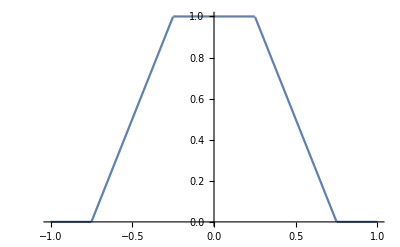

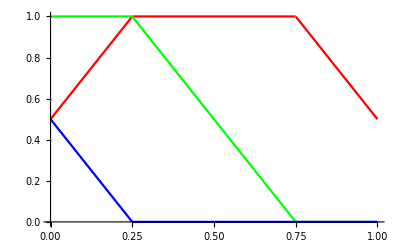

-Graphics-

```mathematica
interpolate[val_,y0_,x0_,y1_,x1_]:=(val-x0)*(y1-y0)/(x1-x0)+y0;
base[val_]:=Piecewise[{
{0,val<-0.75},
{interpolate[val,0.0,-0.75,1.0,-0.25],val<-0.25},
{1,val<0.25},
{interpolate[val,1.0,0.25,0.0,0.75],val<0.75},
{0,True}
}];

Plot[{base[s]},{s,-1,1}]
c[s_]:={base[s-0.5],base[s],base[s+0.5]}
Plot[Evaluate@c[s],{s,0,1},PlotStyle->{Red,Green,Blue}]
Image@Table[c[s],100,{s,0,1,0.01}]
```

```mathematica
Image@{{{0,255,0}}}
```

-Graphics-